# Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["MethodSugiyama`"]
```

```mathematica
?"MethodSugiyama`*"
```

# Help

## 0. GetGraph

```mathematica
??GetGraph
```

```mathematica
g=GetGraph[10]
```

-Graphics-

## 1. GetDaG - удаление циклов

```mathematica
??GetDAG
```

```mathematica
GetDAG[g,ApproachOption->"Unknown"]
```

GetDAG::option: Option Unknown is not in list of options. Choose another one from the list: 
Random Order
BFS Order
DFS Order
VertexOutDegree Order
Cycle Removal
IP SCF
IP TI

$Aborted

```mathematica
GetDAG[g,ApproachOption->"Random Order"]
```

<|acyclic graph→{1->3,2->5,7->5,8->1,8->3,8->6,8->7,10->4,10->7,10->9},feedback set→{1->8,1->10,2->8,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,7->10,9->7}|>

```mathematica
GetDAG[g,ApproachOption->"BFS Order"]
```

<|acyclic graph→{1->3,1->8,1->10,3->5,3->7,5->9,6->2,8->6,8->7,10->4,10->7,10->9},feedback set→{2->5,2->8,4->1,4->5,4->6,5->10,7->5,7->10,8->1,8->3,9->7}|>

```mathematica
GetDAG[g,ApproachOption->"DFS Order"]
```

<|acyclic graph→{1->3,2->5,2->8,4->1,5->9,5->10,6->2,8->1,8->3,8->7,9->7,10->4,10->7},feedback set→{1->8,1->10,3->5,3->7,4->5,4->6,7->5,7->10,8->6,10->9}|>

```mathematica
GetDAG[g,ApproachOption->"VertexOutDegree Order"]
```

<|acyclic graph→{1->3,4->1,4->5,4->6,5->9,7->5,8->1,8->3,8->6,8->7,10->7,10->9},feedback set→{1->8,1->10,2->5,2->8,3->5,3->7,5->10,6->2,7->10,9->7,10->4}|>

```mathematica
step1=GetDAG[g,ApproachOption->"Cycle Removal"]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4}|>

```mathematica
GetDAG[g,ApproachOption->"IP SCF"]
```

<|acyclic graph→{1->3,1->10,2->5,2->8,3->5,3->7,4->1,4->5,4->6,5->9,5->10,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,6->2,7->5,7->10,10->4}|>

```mathematica
GetDAG[g,ApproachOption->"IP TI"]
```

<|acyclic graph→{1->3,1->8,1->10,2->5,2->8,3->5,3->7,4->5,5->10,6->2,7->5,7->10,9->7},feedback set→{4->1,4->6,5->9,8->1,8->3,8->6,8->7,10->4,10->7,10->9}|>

## 2. GetLayering

```mathematica
??GetLayering
```

```mathematica
GetLayering[step1,ApproachOption->"Unknown"]
```

GetLayering::option: Option Unknown is not in list of options. Choose another one from the list: 
Longest Path
Exact
Min Width

$Aborted

```mathematica
step2=GetLayering[step1,ApproachOption->"Longest Path"]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},layers→{{4,8},{1,6},{2,3},{5},{10},{9},{7}}|>

```mathematica
GetLayering[step1,ApproachOption->"Exact"]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},layers→{{4,8},{1,6},{2,3},{5},{10},{9},{7}}|>

```mathematica
GetLayering[step1,ApproachOption->"Min Width"]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},layers→{{8,4},{1,6},{3,2},{5},{10},{9},{7}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",6,2}]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},layers→{{8,4},{1,6},{3,2},{5},{10},{9},{7}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",6,2},ImprovmentOption->"Unk"]
```

GetLayering::option: Option Unk is not in list of options. Choose another one from the list: 
True
False

$Aborted

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",6,2},ImprovmentOption->True]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},layers→{{8,4,6},{1,2},{3},{5,10},{9},{7}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",6,2},ImprovmentOption->False]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},layers→{{8,4},{1,6},{3,2},{5},{10},{9},{7}}|>

## 3. AddDummyVertices

```mathematica
??AddDummyVertices
```

```mathematica
AddDummyVertices[step2,ApproachOption->"Unk"]
```

AddDummyVertices::option: Option Unk is not in list of options. Choose another one from the list: 
Base
Cut

$Aborted

```mathematica
AddDummyVertices[step2,ApproachOption->"Base"]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},graph with dummies→{1->3,2->5,3->5,4->1,4->6,5->10,6->2,8->1,8->6,9->7,10->9,1->11,11->12,12->10,3->13,13->14,14->15,15->7,4->16,16->17,17->5,5->18,18->9,8->19,19->3,8->20,20->21,21->22,22->23,23->24,24->7,10->25,25->7,8->26,26->2,5->27,27->28,28->7,4->29,29->30,30->31,31->10},layers with dummies→{{4,8},{1,6,16,19,20,26,29},{3,2,11,17,21,30},{5,12,13,22,31},{10,14,18,23,27},{9,15,24,25,28},{7}},first dummy→11|>

```mathematica
step3=AddDummyVertices[step2,ApproachOption->"Cut"]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},layers→{{4,8},{1,6},{2,3},{5},{10},{9},{7}},first dummy→11,layers with dummies→{{4,8},{1,6,11,14,19,22,23},{3,2,12,15,20},{5,13,16},{10,17,21},{9,18},{7}},graph with dummies→{1->3,2->5,3->5,4->1,4->6,5->10,6->2,8->1,8->6,9->7,10->9,1->12,4->11,11->12,12->13,13->10,3->16,8->14,10->18,5->17,14->15,15->16,16->17,17->18,18->7,4->19,19->20,20->5,5->21,21->9,8->22,22->3,8->23,23->2}|>

## 4. GetVertexOrder

```mathematica
??GetVertexOrder
```

```mathematica
GetVertexOrder[step3,ApproachOption->"Unk"]
```

GetVertexOrder::option: Option Unk is not in list of options. Choose another one from the list: 
Barycenter
Matheuristic
{Barycenter,maxNumberOfIterations_Integer?Positive}

$Aborted

```mathematica
GetVertexOrder[step3,ApproachOption->"Barycenter"]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},graph with dummies→{1->3,2->5,3->5,4->1,4->6,5->10,6->2,8->1,8->6,9->7,10->9,1->12,4->11,11->12,12->13,13->10,3->16,8->14,10->18,5->17,14->15,15->16,16->17,17->18,18->7,4->19,19->20,20->5,5->21,21->9,8->22,22->3,8->23,23->2},layers with dummies→{{8,4},{14,22,23,6,1,19,11},{15,3,2,20,12},{16,5,13},{17,21,10},{18,9},{7}},first dummy→11|>

```mathematica
GetVertexOrder[step3,ApproachOption->"Matheuristic"]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},graph with dummies→{1->3,2->5,3->5,4->1,4->6,5->10,6->2,8->1,8->6,9->7,10->9,1->12,4->11,11->12,12->13,13->10,3->16,8->14,10->18,5->17,14->15,15->16,16->17,17->18,18->7,4->19,19->20,20->5,5->21,21->9,8->22,22->3,8->23,23->2},layers with dummies→{MethodSugiyama`Private`firstLayer$35309,Join[Complement[{1,6,11,14,19,22,23},Tally[MethodSugiyama`Private`ys$35309]⟦All,1⟧],Tally[MethodSugiyama`Private`ys$35309]⟦All,1⟧],{20,15,3,12,2},{16,5,13},{17,21,10},{18,9},{7}},first dummy→11|>

```mathematica
step4=GetVertexOrder[step3,ApproachOption->{"Barycenter",10}]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},graph with dummies→{1->3,2->5,3->5,4->1,4->6,5->10,6->2,8->1,8->6,9->7,10->9,1->12,4->11,11->12,12->13,13->10,3->16,8->14,10->18,5->17,14->15,15->16,16->17,17->18,18->7,4->19,19->20,20->5,5->21,21->9,8->22,22->3,8->23,23->2},layers with dummies→{{8,4},{14,22,23,6,1,19,11},{15,3,2,20,12},{16,5,13},{17,21,10},{18,9},{7}},first dummy→11|>

## 5. GetCoordinates

```mathematica
??GetCoordinates
```

```mathematica
GetCoordinates[step4,YDistanceOption->1,XDistanceOption->-1.3,WeightsOption->{1,1,1}]
```

GetCoordinates::option: 
Value -1.3 is not positive real.

$Aborted

```mathematica
GetCoordinates[step4,YDistanceOption->-1.4,XDistanceOption->-1.3,WeightsOption->{1,1,1}]
```

GetCoordinates::option: 
Value -1.4 is not positive real.

$Aborted

```mathematica
GetCoordinates[step4,YDistanceOption->1.3,XDistanceOption->1.8,WeightsOption->{неЧисло,"йоу",1}]
```

GetCoordinates::option2: 
 {неЧисло,йоу,1} is not valid input weights. Please write in this form: {w1, w2, w3}

$Aborted

```mathematica
step5=GetCoordinates[step4,YDistanceOption->1,XDistanceOption->1,WeightsOption->{1,1,1}]
```

<|acyclic graph→{1->3,1->10,2->5,3->5,3->7,4->1,4->5,4->6,5->9,5->10,6->2,8->1,8->3,8->6,8->7,9->7,10->7,10->9},feedback set→{1->8,2->8,7->5,7->10,10->4},first dummy→11,graph with dummies→{1->3,2->5,3->5,4->1,4->6,5->10,6->2,8->1,8->6,9->7,10->9,1->12,4->11,11->12,12->13,13->10,3->16,8->14,10->18,5->17,14->15,15->16,16->17,17->18,18->7,4->19,19->20,20->5,5->21,21->9,8->22,22->3,8->23,23->2},layers with dummies→{{8,4},{14,22,23,6,1,19,11},{15,3,2,20,12},{16,5,13},{17,21,10},{18,9},{7}},coords→{8→{-2,-1},4→{-4,-1},14→{0,-2},22→{-1,-2},23→{-2,-2},6→{-3,-2},1→{-4,-2},19→{-5,-2},11→{-6,-2},15→{0,-3},3→{-2,-3},2→{-3,-3},20→{-4,-3},12→{-5,-3},16→{-2,-4},5→{-3,-4},13→{-4,-4},17→{-2,-5},21→{-3,-5},10→{-4,-5},18→{-2,-6},9→{-3,-6},7→{-2,-7}}|>

### Визуализация

```mathematica
Clear[graphPlotNaive]
graphPlotNaive[args_,opts:OptionsPattern[]]:=With[
{vertices=GroupBy[Flatten@args["layers with dummies"],#<args["first dummy"]&]},
Graph[args["graph with dummies"],
VertexCoordinates->args["coords"],
VertexSize->Thread[vertices[False]->0],
VertexLabels->Thread[vertices[True]->vertices[True]],
VertexShapeFunction-> "Triangle",
opts
]
]
```

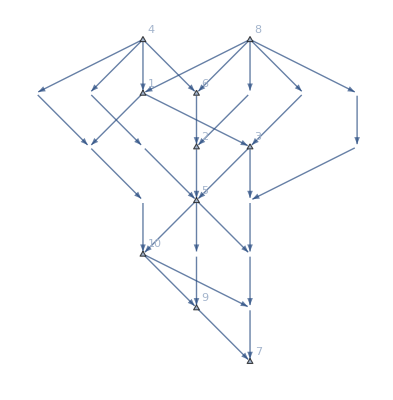

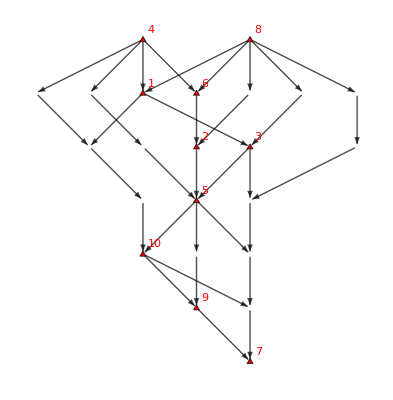

```mathematica
graphPlotNaive[step5]
graphPlotNaive[step5,VertexStyle->Red,EdgeStyle->Black]
```

## 6. Итоговая функция

```mathematica
??MyLayeredGraphPlot
```

```mathematica
g
```

-Graphics-

Done GetDag

Done GetLayering

Done GetAddDummyVertics

Done GetVertexOrder

Done GetCoords

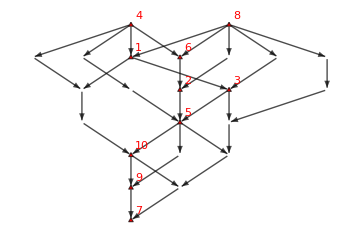

```mathematica
res=MyLayeredGraphPlot[g,input,ApproachOption->"WM"]
```

Done GetDag

Done GetLayering

Done GetAddDummyVertics

Done GetVertexOrder

Done GetCoords

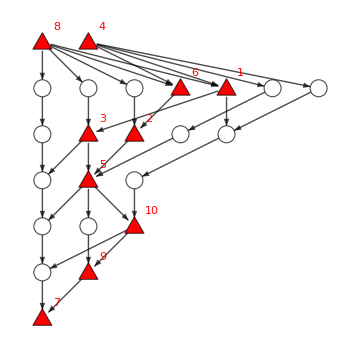

```mathematica
input=<|
"GetDag"-><|"ApproachOption"->"Cycle Removal"|>, 
"GetLayering"-> <|"ApproachOption"->"Longest Path",
                                    "ImprovmentOption"->False|>,
"AddDummyVertices"-><|"ApproachOption"->"Cut"|>,
"GetVertexOrder"-><|"ApproachOption"->{"Barycenter",5}|>,
"GetCoordinates"-> <|"YDistanceOption"->1,
                                           "XDistanceOption"->1.5,
                                            "WeightsOption"->{1,1,1}|>
|>;
res=MyLayeredGraphPlot[g,input,ApproachOption->"Naive"]
```